```mathematica
mosquito population dynamics include Early instars, layter instars, pupae, and adults female.
```

```mathematica
ClearAll[A,P,L,M,K];
```

```mathematica
K[t_]:=10000*(0.5+0.5*Sin[2π*(t/120+30/120)])+100;
f[t_]:=Piecewise[{{K[t],180<Mod[t,360]<300}},100];
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]);
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ));
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,330<t<420||540<t<630||750<t<900}},MuM0];
```

```mathematica
MuM0=0.096;
```

```mathematica
f[t_]:=Piecewise[{{K[t],180<Mod[t,360]<300}},100];
```

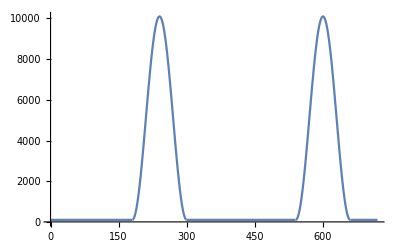

```mathematica
Plot[f[t],{t,0,720}]
```

```mathematica
f1[t_]:=f[Mod[t,360]]
```

```mathematica
f1[360.1]
```

100

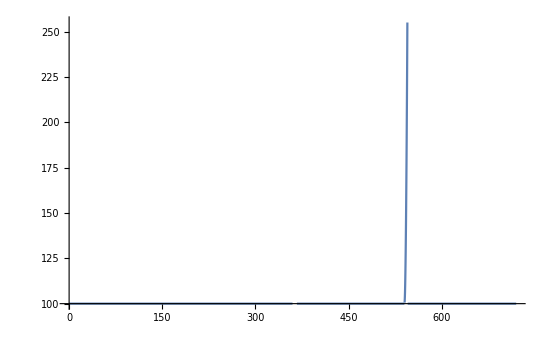

```mathematica
Plot[f1[t],{t,0,720}]
```

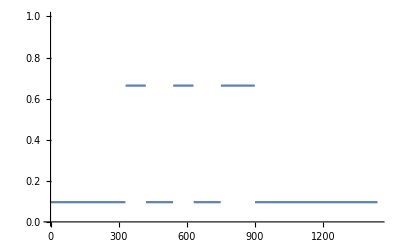

```mathematica
Plot[Evaluate[MuM[0.8,0.92,0.97,0.207,0.86,t]],{t,0,1440},PlotRange->{0,1}]
```

```mathematica
MuM[0.8,0.92,0.97,0.207,0.86,300]
```

0.096

```mathematica
β=25;
de=6.64;
dl=3.72;
dp=0.64;
MuM0=0.096;
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t],
L'[t]==A[t]/de-MuL[t]*L[t]-L[t]/dl,
P'[t]==L[t]/dl-0.25P[t]-P[t]/dp,
M'[t]==0.5*P[t]/dp-MuM[0.8,0.92,0.97,0.207,0.86,t]*M[t],

M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
}
```

{A'[t]==-0.150602 A[t]+25 M[t]-0.035 A[t] (1+(A[t]+L[t])/Piecewise[{{100+10000 (0.5+0.5 Sin[2 π (1/4+t/120)]), 180<Mod[t,360]<300}, {100, True}}]),L'[t]==0.150602 A[t]-0.268817 L[t]-0.035 L[t] (1+(13.25 (A[t]+L[t]))/Piecewise[{{100+10000 (0.5+0.5 Sin[2 π (1/4+t/120)]), 180<Mod[t,360]<300}, {100, True}}]),P'[t]==0.268817 L[t]-1.8125 P[t],M'[t]==0.78125 P[t]-M[t] (Piecewise[{{0.663417, 330<t<420||540<t<630||750<t<900}, {0.096, True}}]),M[0]==10,A[0]==100,P[0]==500,L[0]==200}

```mathematica
sol = NDSolve[system,{A[t],P[t],L[t],M[t]},{t,0,1440}]
```

{{A[t]→InterpolatingFunction[{{0., 1440.}}, <>][t],P[t]→InterpolatingFunction[{{0., 1440.}}, <>][t],L[t]→InterpolatingFunction[{{0., 1440.}}, <>][t],M[t]→InterpolatingFunction[{{0., 1440.}}, <>][t]}}

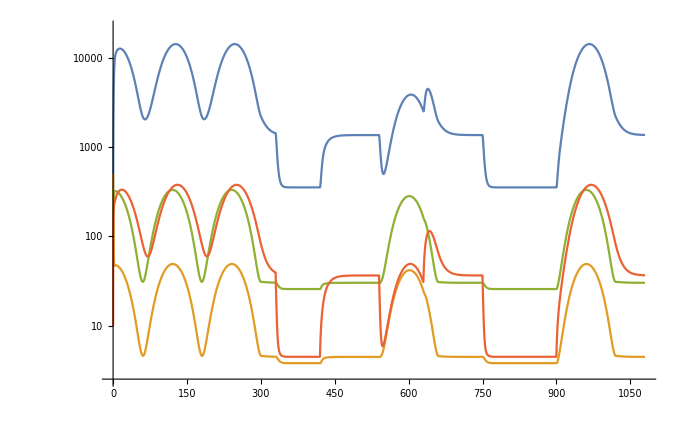

```mathematica
LogPlot[Evaluate[{A[t],P[t],L[t],M[t]}/.sol],{t,0,1080}]
```

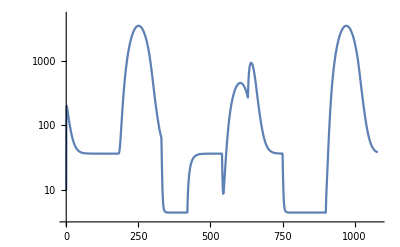

```mathematica
LogPlot[Evaluate[{M[t]}/.sol],{t,0,1080}]
```

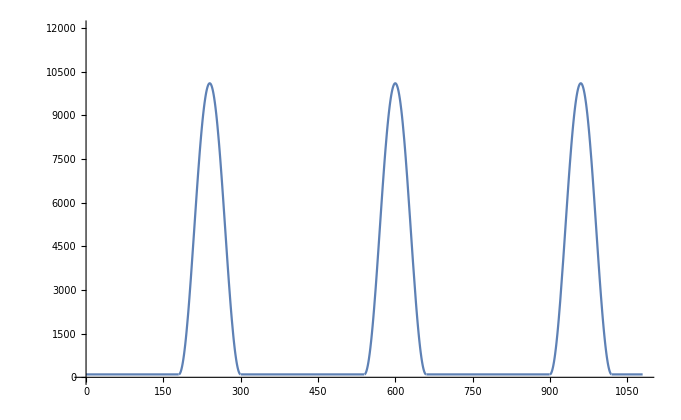

```mathematica
Plot[f[t],{t,0,1080},PlotRange->{0,12000}]
```